```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
DiMauro={{0.11592770333719869 ,1.430902724036737*10^-7 },{0.1552419727919801,1.3179420496721543*10^-7},{0.20454943547538015,8.583697005721025*10^-8},{0.2761483125230999,9.429532155412788*10^-8},{0.36803607894880785,1.5174694782872762*10^-7},{0.48679704343252744,2.3027136175334634*10^-7},{0.6526663609063482,2.762615710198307*10^-7},{0.868657027321059,3.2949591880051146*10^-7},{1.164235975134054,3.6624168819479853*10^-7},{1.5487794318504893,3.9298828318905065*10^-7},{2.073515175360936,3.4332619284070296*10^-7},{2.756110370684767,3.0707058382385326*10^-7},{3.6645869109432856,2.9470080134723354*10^-7},{4.938211547069397,2.15863437995542*10^-7},{6.609896317259527,1.7992791265356413*10^-7},{8.653956168958699,1.4393323808133127*10^-7},{11.585659239935609,1.250078960579582*10^-7},{15.282166070975402,1.0358715668866392*10^-7},{20.457126458496873,8.787762697302056*10^-8},{27.388854044575474,7.722477322409351*10^-8},{36.36344700262212,5.3653189668710636*10^-8},{48.734279516882474,5.8940160269446834*10^-8},{65.21964092744737,4.714914987619674*10^-8},{86.75685271001828,5.000157918665334*10^-8}};
Zhong12={{0.2698936461850911,2.0235896477251556*10^-8},{0.4031852049908963,5.55773658648687*10^-8},{0.5306041497635453,8.286427728546843*10^-8},{0.6836949708649847,9.319395762340776*10^-8},{0.8809558187480787,7.722449945836255*10^-8},{1.1593649950439693,1.2067926406393264*10^-7},{1.493866975713819,1.2949258422052604*10^-7},{1.965974958149487,1.52641796717523*10^-7},{2.5332014314857654,1.4563484775012414*10^-7},{3.3337711183217964,1.5627069765469932*10^-7},{4.205844492778353,1.4563484775012414*10^-7},{7.284258025108297,8.68511373751352*10^-8},{51.951289318465555;3.23745754281764*10^-8}};
Calore={{{0.3204486923217852,6.9564960995706185*10^-9},ErrorBar[1.2648552168552983*10^-7,5.261243901795341*10^-9]},{{0.3759635927148633,5.6521774773949544*10^-8},ErrorBar[1.67683293681101*10^-7,4.291934260128787*10^-8]},{{0.41753189365604004,5.870937850692427*10^-8},ErrorBar[1.7575106248547964*10^-7,4.641588833612791*10^-8]},{{0.4605597747647078,7.425886368281534*10^-8},ErrorBar[1.9006912028137782*10^-7,5.779692884153325*10^-8]},{{0.5224596297751556,8.28642772854686*10^-8},ErrorBar[(*3.556480306223136*10^-7*) 1.9006912028137782*10^-7,6.551285568595522*10^-8]},{{0.5844323938042159,2.0879874845047515*10^-7},ErrorBar[3.288567819970276*10^-7,8.96150501946605*10^-8]},{{0.6556985133819497,2.5967438685878555*10^-7},ErrorBar[3.7275937203149455*10^-7,1.3051074191219142*10^-7]},{{0.7475885795969246,2.0574088705192087*10^-7},ErrorBar[3.1871416115850785*10^-7,9.691579392800516*10^-8]},{{0.8531678524172814,2.9935772947204905*10^-7},ErrorBar[4.0949150623804273*10^-7,1.7575106248547964*10^-7]},{{0.9855215688383892,2.9648599685278553*10^-7},ErrorBar[4.0949150623804273*10^-7,4.498432668969453*10^-7]},{{1.1387901130668405,3.4600097472326136*10^-7},ErrorBar[4.498432668969453*10^-7,2.1884471064600369*10^-7]},{{1.3317708758407547,3.6002561319062116*10^-7},ErrorBar[4.5694501687891855*10^-7,2.641001862504401*10^-7]},{{1.6149512770943755,3.2538091209159305*10^-7},ErrorBar[4.1595621630718514*10^-7,2.3667351447252376*10^-7]},{{1.9291989145345407,3.9859764927376447*10^-7},ErrorBar[4.789300737773289*10^-7,3.0888435964774847*10^-7]},{{2.2947423401149027,3.541113510035906*10^-7},ErrorBar[4.498432668969453*10^-7,2.768068739417855*10^-7]},{{2.926352575600284,3.3897972273636966*10^-7},ErrorBar[4.225229858223504*10^-7,2.599955928668555*10^-7]},{{3.737141937450008,3.316333172539281*10^-7},ErrorBar[3.968619443383451*10^-7,2.6826957952797275*10^-7]},{{5.094806239666136,2.909218779465988*10^-7},ErrorBar[3.556480306223136*10^-7,2.329951810515372*10^-7]},{{7.157154694129966,1.7752688336350715*10^-7},ErrorBar[2.2580912953008987*10^-7,1.2848236951554498*10^-7]},{{10.018497226843353,2.1426863106901705*10^-7},ErrorBar[2.641001862504401*10^-7,1.574994028640114*10^-7]},{{15.794220821098424,1.0308061514091419*10^-7},ErrorBar[1.5026946780037864*10^-7,5.779692884153325*10^-8]},{{28.193766915612823,9.411434162314103*10^-8},ErrorBar[1.2451970847350344*10^-7,6.153407071116611*10^-8]},{{62.79922353366887,5.360538616292313*10^-8},ErrorBar[8.030857221391537*10^-8,2.188447106460037*10^-8]}};

(*ErrorCalore=Total[{Calore,CaloreERR.DiagonalMatrix[{0,-1}]}]*)
Zhong1={{0.2756556969794437;2.5595479226995333*10^-8},{0.41179294238496555;7.906043210907701*10^-8},{0.5306041497635453;1.2648552168552957*10^-7},{0.6836949708649847;1.5998587196060571*10^-7},{0.8809558187480787;1.389495494373136*10^-7},{1.1593649950439693;1.8420699693267125*10^-7},{1.525760047357919;1.8858632787726476*10^-7},{1.965974958149487;1.9765980717016307*10^-7},{2.5332014314857654;1.7575106248547896*10^-7},{3.3337711183217964;1.8858632787726476*10^-7},{4.295636490267305;1.7992936232915516*10^-7},{7.439772114947442;1.0730309405261565*10^-7},{51.951289318465555;3.906939937054621*10^-8}};

(*We want to interpolate using the following function*)
```

```mathematica
POINTS=Calore;
(*PointsErrors=ErrorCalore . {0,1};*)
(*PointsErrors=POINTS . {0,0.32};*)

Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)

Clear[F1,F];
F[x_]=Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,F0  F[x],F0,x(*,Weights->1/PointsErrors^2*)]
(*F1[x_]=Fit[DiMauro,F[x],x]*)

Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```

NonlinearModelFit::fitd: First argument {{{0.320449,6.9565×10^-9},ErrorBar[1.26486×10^-7,5.26124×10^-9]},{{0.375964,5.65218×10^-8},ErrorBar[1.67683×10^-7,4.29193×10^-8]},{{0.417532,5.87094×10^-8},ErrorBar[1.75751×10^-7,4.64159×10^-8]},{{0.46056,7.42589×10^-8},ErrorBar[1.90069×10^-7,5.77969×10^-8]},{{0.52246,8.28643×10^-8},ErrorBar[1.90069×10^-7,6.55129×10^-8]},«14»,{{10.0185,2.14269×10^-7},ErrorBar[2.641×10^-7,1.57499×10^-7]},{{15.7942,1.03081×10^-7},ErrorBar[1.50269×10^-7,5.77969×10^-8]},{{28.1938,9.41143×10^-8},ErrorBar[1.2452×10^-7,6.15341×10^-8]},{{62.7992,5.36054×10^-8},ErrorBar[8.03086×10^-8,2.18845×10^-8]}} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{{{0.320449,6.9565×10^-9},ErrorBar[1.26486×10^-7,5.26124×10^-9]},{{0.375964,5.65218×10^-8},ErrorBar[1.67683×10^-7,4.29193×10^-8]},{{0.417532,5.87094×10^-8},ErrorBar[1.75751×10^-7,4.64159×10^-8]},{{0.46056,7.42589×10^-8},ErrorBar[1.90069×10^-7,5.77969×10^-8]},{{0.52246,8.28643×10^-8},ErrorBar[1.90069×10^-7,6.55129×10^-8]},{{0.584432,2.08799×10^-7},ErrorBar[3.28857×10^-7,8.96151×10^-8]},{{0.655699,2.59674×10^-7},ErrorBar[3.72759×10^-7,1.30511×10^-7]},{{0.747589,2.05741×10^-7},ErrorBar[3.18714×10^-7,9.69158×10^-8]},{{0.853168,2.99358×10^-7},ErrorBar[4.09492×10^-7,1.75751×10^-7]},{{0.985522,2.96486×10^-7},ErrorBar[4.09492×10^-7,4.49843×10^-7]},{{1.13879,3.46001×10^-7},ErrorBar[4.49843×10^-7,2.18845×10^-7]},{{1.33177,3.60026×10^-7},ErrorBar[4.56945×10^-7,2.641×10^-7]},{{1.61495,3.25381×10^-7},ErrorBar[4.15956×10^-7,2.36674×10^-7]},{{1.9292,3.98598×10^-7},ErrorBar[4.7893×10^-7,3.08884×10^-7]},{{2.29474,3.54111×10^-7},ErrorBar[4.49843×10^-7,2.76807×10^-7]},{{2.92635,3.3898×10^-7},ErrorBar[4.22523×10^-7,2.59996×10^-7]},{{3.73714,3.31633×10^-7},ErrorBar[3.96862×10^-7,2.6827×10^-7]},{{5.09481,2.90922×10^-7},ErrorBar[3.55648×10^-7,2.32995×10^-7]},{{7.15715,1.77527×10^-7},ErrorBar[2.25809×10^-7,1.28482×10^-7]},{{10.0185,2.14269×10^-7},ErrorBar[2.641×10^-7,1.57499×10^-7]},{{15.7942,1.03081×10^-7},ErrorBar[1.50269×10^-7,5.77969×10^-8]},{{28.1938,9.41143×10^-8},ErrorBar[1.2452×10^-7,6.15341×10^-8]},{{62.7992,5.36054×10^-8},ErrorBar[8.03086×10^-8,2.18845×10^-8]}},F0 (Piecewise[{{2.79056 x^0.58, x<2.06}, {6.69069/x^0.63, x>2.06}, {0, True}}]),F0,x]

General::ivar: 0.100014 is not a valid variable.

General::ivar: 0.115156 is not a valid variable.

General::ivar: 0.13259 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
NIntegrate[F1[x]/x^2,{x,0.1,100}] 0.00160218
```

2.11314×10^-10

FittedModel[Piecewise[{{2.96402×10^-7 x^0.378373, x<1.98152}, {(5.89005×10^-7)/x^0.625804, x>1.98152}, {0, True}}]]

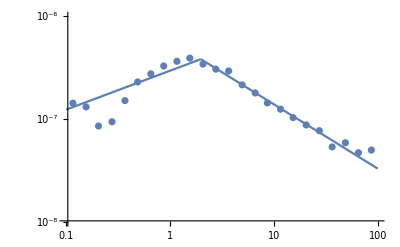

```mathematica
Clear[F0,n1,n2,Eb];
F[x_]=  Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2 F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,{F[x],Eb>0},{F0,{n1,1.41},{n2,2.63},{Eb,2.06}},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{10^-8,10^-6}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}}]]
```

FittedModel[Piecewise[{{2.94163×10^-7 x^0.455388, x<2.06}, {(6.68131×10^-7)/x^0.679722, x>2.06}, {0, True}}]]

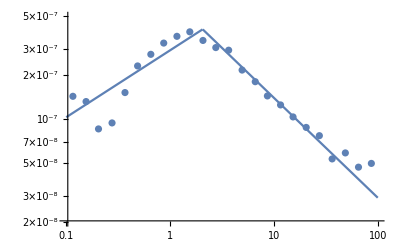

3.92597×10^-7 (Piecewise[{{0.743557 x^0.41, x<2.06}, {1.57665/x^0.63, x>2.06}, {0, True}}])

```mathematica
Clear[F0,n1,n2];
Eb=2.06;
F[x_]=Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2  F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,F[x],{F0,n1,n2},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```